```mathematica
(* Ladder Network Analysis*)
```

```mathematica
(* Error Rate *)
η[λ_,μ_,Δ_,n_]:=ⅇ^-Δ(((μ/λ)^(n+1)-1)/((μ/λ)^(n+1)ⅇ^((n+1)Δ)-1)((μ/λ) ⅇ^Δ-1)/((μ/λ)-1))
```

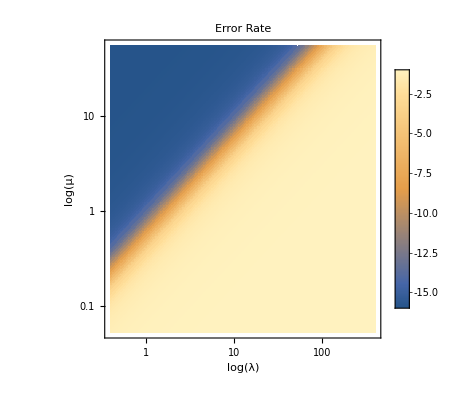

```mathematica
DensityPlot[Log[η[Λ,Μ,1,15]],{Λ,0,ⅇ^6},{Μ,0,ⅇ^4},FrameLabel->{Log[λ],Log[μ]},PlotPoints->100,ScalingFunctions->{"Log","Log"},PlotRange->Full,PlotTheme->"Detailed",PlotLabel->"Error Rate"]
```

```mathematica
(* Mean First Passage Time *)
Subscript[T, R][λ_,μ_,Δ_,n_]:=(n+2)λ((2(μ/λ)^(n+2)-(2n+1)(μ/λ)^2+2(n-1)(μ/λ)+1)/((μ/λ)-1)^2)
```

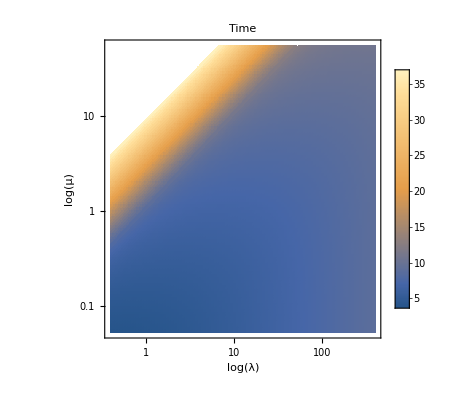

```mathematica
DensityPlot[Log[Subscript[T, R][Λ,Μ,1,15]],{Λ,0,ⅇ^6},{Μ,0,ⅇ^4},FrameLabel->{Log[λ],Log[μ]},PlotPoints->100,ScalingFunctions->{"Log","Log"},PlotTheme->"Detailed",PlotLabel->"Time"]
```

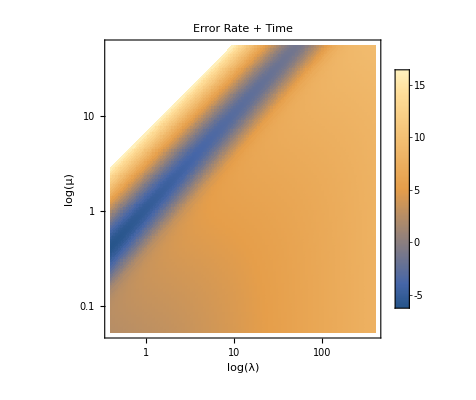

```mathematica
(* Combination Plot where the lower the number corresponds to a lower error rate and a fast time -> shows the line that minimizes both time and error rate *)
DensityPlot[Log[Subscript[T, R][Λ,Μ,1,15]]+Log[η[Λ,Μ,1,15]],{Λ,0,ⅇ^6},{Μ,0,ⅇ^4},FrameLabel->{Log[λ],Log[μ]},PlotPoints->100,ScalingFunctions->{"Log","Log"},PlotTheme->"Detailed",PlotLabel->"Error Rate + Time"]
```